# Discrete Calculus

```mathematica
RunScheduledTask[NotebookSave[EvaluationNotebook[]],30]
```

ScheduledTaskObject[…]

## 1. Intro

keywords : sequences/series, finite differences, sums/products, gfun
e . g . Finite Sums / Infinite Sums,    Riemann Sums

```mathematica
∑_(k=0)^5 k  
∑_(k=1)^∞ 1/2^k
f[x_]=(x-1)^(1/3); plot=Plot[f[x],{x,0,3},AspectRatio->Automatic,PlotTheme->"Detailed"]
Show[DiscretePlot[f[x],{x,1,3,1/3},ExtentSize->Full],plot]
```

15

1

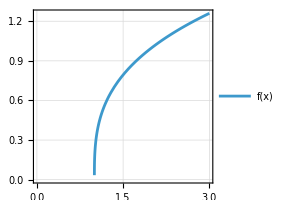

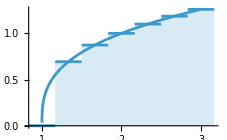

-Graphics-

#### Sigma Notation

Basic Examples

```mathematica
∑_(k=0)^5 k
```

15

Infinite Sums

```mathematica
∑_(k=1)^∞ 1/2^k
```

1

```mathematica
∑_(k=0)^∞ 1/(k!)
```

ⅇ

#### Riemann Sums

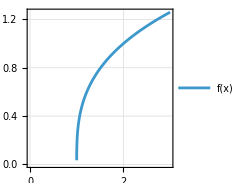

```mathematica
f[x_]=(x-1)^(1/3);
plot=Plot[f[x],{x,0,3},AspectRatio->Automatic,PlotTheme->"Detailed"]
```

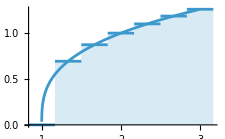

```mathematica
Show[DiscretePlot[f[x],{x,1,3,1/3},ExtentSize->Full],plot]
```

```mathematica
N[∑_(k=1)^6 f[1+((3-1)/6)k]*((3-1)/6)]
```

2.03771

#### Product Notation

```mathematica
∏_(k=1)^5 k
```

```mathematica
120
```

```mathematica
N[∏_(k=2)^∞ ((k^2-1)/k^2)^(2(k^2-1))((k+1)/(k-1))^k]
```

```mathematica
3.0899225749115415
```

#### Taylor Series

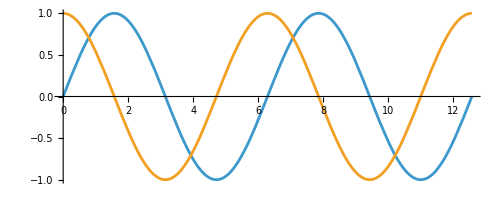

```mathematica
f[x_]=∑_(k=0)^∞ ((-1)^k x^(2k+1))/((2k+1)!);
g[x_]=∑_(k=0)^∞ ((-1)^k x^(2k))/((2k)!);
Plot[{f[x],g[x]},{x,0,4π},AspectRatio->Automatic]
```

```mathematica
f[x_]=x∏_(k=1)^∞ (1-x^2/(k^2 π^2));
g[x_]=∏_(k=1)^∞ (1-(4 x^2)/(π^2(2k-1)^2));
Plot[{f[x],g[x]},{x,0,4π},AspectRatio->Automatic]
```

-Graphics-

#### Finite Differences

```mathematica
f[x_]=4x-5 x^2+x^3;
plot=Plot[f[x],{x,-0.5,4.25},AspectRatio->Automatic]
difForward[x_,h_]=(f[x+h]-f[x])/h
difBackward[x_,h_]=(f[x]-f[x-h])/h
difCentral[x_,a_]=(f[x+a]-f[x-a])/(2a)
```

-Graphics-

(-4 x+5 x^2-x^3+4 (h+x)-5 (h+x)^2+(h+x)^3)/h

(4 x-5 x^2+x^3-4 (-h+x)+5 (-h+x)^2-(-h+x)^3)/h

(-4 (-a+x)+5 (-a+x)^2-(-a+x)^3+4 (a+x)-5 (a+x)^2+(a+x)^3)/(2 a)

```mathematica
(*coding form*)
f'[x]
Limit[difForward[x,h],h->0]
Limit[difBackward[x,h],h->0]
Simplify[Limit[difCentral[x,h],h->0]]
```

4-10 x+3 x^2

4-10 x+3 x^2

4-10 x+3 x^2

«1 more identical outputs»

```mathematica
(*math form*)
f'(x)
difForward(x,h)h0
difBackward(x,h)h0
Simplify[difCentral(x,h)h0]
```

4-10 x+3 x^2

4-10 x+3 x^2

4-10 x+3 x^2

«1 more identical outputs»

## 2. Number Theory

```mathematica
Divisible[10,5]
Mod[12,10](*cannot use %*)
```

True

2

```mathematica
a=420;   (*separate input cell*)
b=860;
```

```mathematica
(*repeat until output appears*)
r=Mod[a,b];
a=b;
If[r>0,b=r,Print[a]];
```

20

```mathematica
(*only need to run once*)
r=Mod[a,b];
a=b;
While[r>0,b=r;r=Mod[a,b];a=b]
Print[a]
```

20

```mathematica
GCD[a,b]
```

20

## 3. Primes

## Basic Things

```mathematica
Table[Prime[i],{i,10}]
```

{2,3,5,7,11,13,17,19,23,29}

```mathematica
PrimeQ[67]
PrimeQ[267]
CompositeQ[6767]
CompositeQ[673]
```

True

False

True

False

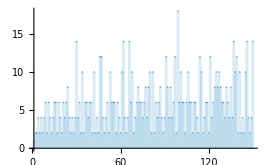

```mathematica
gap[n_]=Prime[n+1]-Prime[n];
DiscretePlot[gap[n],{n,150}]
```

```mathematica
RandomPrime[100]
```

73

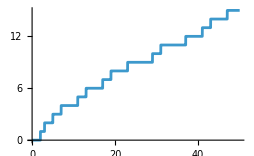

```mathematica
Plot[PrimePi[x],{x,0,50}]
```

## Applications

```mathematica
(*RSA Encryption*)
p=Prime[18];
q=Prime[16];
n=p*q
```

3233

```mathematica
EulerPhi[n]
u=17;
k=15;
CoprimeQ[u,EulerPhi[n]]
PrivKey=(k*EulerPhi[n]+1)/u
```

3120

True

2753

```mathematica
data=ToCharacterCode["Secret"]
encrypted=Mod[data^u,n]
```

{83,101,99,114,101,116}

{2680,1313,281,2412,1313,884}

```mathematica
decrypted=Mod[encrypted^PrivKey,n]
```

{83,101,99,114,101,116}

```mathematica
EulerPhi[n]==(p-1)(q-1)
```

True

## 4. Fibonacci

```mathematica
DiscreteAsymptotic[Fibonacci[n]/Fibonacci[n-1],n->∞]
DiscreteAsymptotic[Fibonacci[n],n->∞]
```

GoldenRatio

GoldenRatio^n/(√5)

```mathematica
Table[Fibonacci[i],{i,-20,20}]      (*including 0 is optional*)
```

{-6765,4181,-2584,1597,-987,610,-377,233,-144,89,-55,34,-21,13,-8,5,-3,2,-1,1,0,1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

```mathematica
Table[Fibonacci[i,x],{i,-5,5}]
```

{1+3 x^2+x^4,-2 x-x^3,1+x^2,-x,1,0,1,x,1+x^2,2 x+x^3,1+3 x^2+x^4}

```mathematica
Fibonacci[0.5]
OtherRatio=1-GoldenRatio;
N[(√GoldenRatio-√OtherRatio)/(√5)]
```

0.568864

0.568864-0.351578 ⅈ

When Fib inputs expand from integers to continuous, use Euler’s formula to calculate powers.
Sage coding: def a(n): return BinaryRecurrenceSequence(1, 1).period(n)           Lucas sequence is BinaryRecurrenceSequence and Fib is special Lucas

```mathematica
test[{0, 1, _}]:= False; test[_]:= True;
nest[k_][{a_, b_, c_}]:= {Mod[b, k], Mod[a+b, k], c+1};
A001175[1] := 1;
A001175[k_]:= NestWhile[nest[k], {1, 1, 1}, test][[3]];
Table[A001175[n], {n, 100}] (* Leo C. Stein, Nov 08 2019 *)
```

{1,3,8,6,20,24,16,12,24,60,10,24,28,48,40,24,36,24,18,60,16,30,48,24,100,84,72,48,14,120,30,48,40,36,80,24,76,18,56,60,40,48,88,30,120,48,32,24,112,300,72,84,108,72,20,48,72,42,58,120,60,30,48,96,140,120,136,36,48,240,70,24,148,228,200,18,80,168,78,120,216,120,168,48,180,264,56,60,44,120,112,48,120,96,180,48,196,336,120,300}

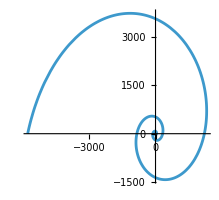

```mathematica
PolarPlot[GoldenRatio^(2θ/π),{θ,0,9π}]
```

-Graphics-

## 5. Permutations and Combinations

```mathematica
Perm[n_,k_]=n!/(n-k)!;
Perm[11,11]
```

39916800

```mathematica
Length[Permutations[{1,2,3,4,5,6,7,8,9,10,11}]]
```

39916800

Birthday problem (pigeonhole principle, see Twelvefold Way)

```mathematica
Combinations[n_, k_] = n!/((n-k)!k!);
NumberOfPairs = Combinations[40, 2];
N[(1-(364/365)^NumberOfPairs)*100]
```

88.2336

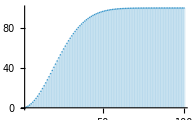

```mathematica
BirthdayChance[n_] =100* (1-((364/365)^Combinations[n, 2]));
DiscretePlot[BirthdayChance[n], {n, 2, 100}]
```

```mathematica
[15]
```

|  |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  | 1 |  | 2 |  | 1 |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  | 1 |  | 3 |  | 3 |  | 1 |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  | 1 |  | 4 |  | 6 |  | 4 |  | 1 |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  | 1 |  | 5 |  | 10 |  | 10 |  | 5 |  | 1 |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 1 |  | 6 |  | 15 |  | 20 |  | 15 |  | 6 |  | 1 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  | 1 |  | 7 |  | 21 |  | 35 |  | 35 |  | 21 |  | 7 |  | 1 |  |  |  |  |  |  | 
 |  |  |  |  |  | 1 |  | 8 |  | 28 |  | 56 |  | 70 |  | 56 |  | 28 |  | 8 |  | 1 |  |  |  |  |  | 
 |  |  |  |  | 1 |  | 9 |  | 36 |  | 84 |  | 126 |  | 126 |  | 84 |  | 36 |  | 9 |  | 1 |  |  |  |  | 
 |  |  |  | 1 |  | 10 |  | 45 |  | 120 |  | 210 |  | 252 |  | 210 |  | 120 |  | 45 |  | 10 |  | 1 |  |  |  | 
 |  |  | 1 |  | 11 |  | 55 |  | 165 |  | 330 |  | 462 |  | 462 |  | 330 |  | 165 |  | 55 |  | 11 |  | 1 |  |  | 
 |  | 1 |  | 12 |  | 66 |  | 220 |  | 495 |  | 792 |  | 924 |  | 792 |  | 495 |  | 220 |  | 66 |  | 12 |  | 1 |  | 
 | 1 |  | 13 |  | 78 |  | 286 |  | 715 |  | 1287 |  | 1716 |  | 1716 |  | 1287 |  | 715 |  | 286 |  | 78 |  | 13 |  | 1 | 
1 |  | 14 |  | 91 |  | 364 |  | 1001 |  | 2002 |  | 3003 |  | 3432 |  | 3003 |  | 2002 |  | 1001 |  | 364 |  | 91 |  | 14 |  | 1

100 Prisoners problem
100 prisoners go into a room one by one and choose 50 cabinets numbered cabinets from 1-100 out of 100 to open. They try to find the one that matches their prisoner number(1-100) inside the 50 cabinets.

Random picking strategy

```mathematica
N[(1/2)^100]
```

7.88861×10^-31

Another strategy is to start with the cabinet that matches their number. Then, if they don’t find their number inside, they go to the cabinet with the number inside the previous one. This way, the prisoner will end up in a permutation cycle. The prisoners win if no cycle is longer than 50. But if they lose, then at least 51 of them lose.

```mathematica
100 * N[1 - (1/(100!) * Sum[(100!)/n, {n, 51, 100}])]
```

31.1828

## 6. Harmonic Numbers

```mathematica
Table[N[HarmonicNumber[i]],{i,100}]
```

{1.,1.5,1.83333,2.08333,2.28333,2.45,2.59286,2.71786,2.82897,2.92897,3.01988,3.10321,3.18013,3.25156,3.31823,3.38073,3.43955,3.49511,3.54774,3.59774,3.64536,3.69081,3.73429,3.77596,3.81596,3.85442,3.89146,3.92717,3.96165,3.99499,4.02725,4.0585,4.0888,4.11821,4.14678,4.17456,4.20159,4.2279,4.25354,4.27854,4.30293,4.32674,4.35,4.37273,4.39495,4.41669,4.43796,4.4588,4.47921,4.49921,4.51881,4.53804,4.55691,4.57543,4.59361,4.61147,4.62901,4.64625,4.6632,4.67987,4.69626,4.71239,4.72827,4.74389,4.75928,4.77443,4.78935,4.80406,4.81855,4.83284,4.84692,4.86081,4.87451,4.88802,4.90136,4.91451,4.9275,4.94032,4.95298,4.96548,4.97782,4.99002,5.00207,5.01397,5.02574,5.03737,5.04886,5.06022,5.07146,5.08257,5.09356,5.10443,5.11518,5.12582,5.13635,5.14676,5.15707,5.16728,5.17738,5.18738}

There are some applications of Harmonic numbers in problems such as card stacking and traffic bunching.

## 7. Partitions

## 8. Bernoulli Numbers

This sequence is somewhat abstract and unintuitive, so we will go over how Bernoulli discovered this.

```mathematica
Grid[Table[{m,Expand[Sum[k^m, {k, 0, n-1}]]}, {m, 0, 10}]]
```

0 | n
1 | -n/2+n^2/2
2 | n/6-n^2/2+n^3/3
3 | n^2/4-n^3/2+n^4/4
4 | -n/30+n^3/3-n^4/2+n^5/5
5 | -n^2/12+(5 n^4)/12-n^5/2+n^6/6
6 | n/42-n^3/6+n^5/2-n^6/2+n^7/7
7 | n^2/12-(7 n^4)/24+(7 n^6)/12-n^7/2+n^8/8
8 | -n/30+(2 n^3)/9-(7 n^5)/15+(2 n^7)/3-n^8/2+n^9/9
9 | -(3 n^2)/20+n^4/2-(7 n^6)/10+(3 n^8)/4-n^9/2+n^10/10
10 | (5 n)/66-n^3/2+n^5-n^7+(5 n^9)/6-n^10/2+n^11/11

S_m(n)=1/(m+1)(B_0 n^(m+1)+(m+1
1)B_1 n^m+...+(m+1
m)B_m n)
S_m(n)=1/(m+1)∑_(k=0)^m ((m+1
k)B_k n^(m+1-k))

```mathematica
Expand[Sum[k^15, {k, 0, n-1}]*(16)]
Table[Coefficient[%, n, i]/Binomial[16, 16-i], {i, 1, 16}]
Reverse[%]
Table[BernoulliB[n], {n, 0, 15}]
```

140 n^2-(1382 n^4)/3+(1820 n^6)/3-429 n^8+(572 n^10)/3-(182 n^12)/3+20 n^14-8 n^15+n^16

{0,7/6,0,-691/2730,0,5/66,0,-1/30,0,1/42,0,-1/30,0,1/6,-1/2,1}

{1,-1/2,1/6,0,-1/30,0,1/42,0,-1/30,0,5/66,0,-691/2730,0,7/6,0}

{1,-1/2,1/6,0,-1/30,0,1/42,0,-1/30,0,5/66,0,-691/2730,0,7/6,0}

```mathematica
Grid[Table[{Subscript[B, n],BernoulliB[n]}, {n, 3, 13, 2}]]
```

B_3 | 0
B_5 | 0
B_7 | 0
B_9 | 0
B_11 | 0
B_13 | 0

Recursive definition: (B^+)_n=1-∑_(k=0)^(n-1) (n
k)B_k/(n-k+1).

```mathematica
Table[Sum[Sum[Binomial[k, v]*(-1)^v*(v+1)^n/(k+1), {v, 0, k}], {k, 0, n}], {n, 1, 15}]
```

{1/2,1/6,0,-1/30,0,1/42,0,-1/30,0,5/66,0,-691/2730,0,7/6,0}

B_n=δ_(n,0)-∑_(k=0)^(n-1) (n
k)B_k/(n-k+1)
 if i=j and 0 otherwise
B_(2n)=(-1)^(n+1)2(2n!)/(2π)^(2n)ζ(2n).
(B^+)_n=-nζ(1-n) for n ≥1.

## 9. Stirling Numbers

Map problem
Suppose that there are 6 markers on a map, and they are all connected by exactly one edge. How many ways are there to visit each marker exactly once(starting point doesn’t matter)?

Stirling numbers(1st kind)
 is the number of ways to separate  objects into  cycles
If ,  
For each new object, add it to an existing cycle or start a new one.
Recurrence relation: 

Stirling numbers(2nd kind)
(this is different) is the number of ways to partition a set of  objects into  subsets
If  or , 
For each new element, add it to an existing subset or a new one.
Recurrence relation:

```mathematica
Abs[StirlingS1[6,1]] (*to verify our solution to the map problem*)
```

120

```mathematica
Grid[Table[{n,Table[Abs[StirlingS1[n, k]], {k, 0, 10}]}, {n,0,10}],Alignment->Left]
```

0 | {1,0,0,0,0,0,0,0,0,0,0}
1 | {0,1,0,0,0,0,0,0,0,0,0}
2 | {0,1,1,0,0,0,0,0,0,0,0}
3 | {0,2,3,1,0,0,0,0,0,0,0}
4 | {0,6,11,6,1,0,0,0,0,0,0}
5 | {0,24,50,35,10,1,0,0,0,0,0}
6 | {0,120,274,225,85,15,1,0,0,0,0}
7 | {0,720,1764,1624,735,175,21,1,0,0,0}
8 | {0,5040,13068,13132,6769,1960,322,28,1,0,0}
9 | {0,40320,109584,118124,67284,22449,4536,546,36,1,0}
10 | {0,362880,1026576,1172700,723680,269325,63273,9450,870,45,1}

```mathematica
Grid[Table[{n,Table[Abs[StirlingS2[n, k]], {k, 0, 10}]}, {n,0,10}],Alignment->Left]
```

0 | {1,0,0,0,0,0,0,0,0,0,0}
1 | {0,1,0,0,0,0,0,0,0,0,0}
2 | {0,1,1,0,0,0,0,0,0,0,0}
3 | {0,1,3,1,0,0,0,0,0,0,0}
4 | {0,1,7,6,1,0,0,0,0,0,0}
5 | {0,1,15,25,10,1,0,0,0,0,0}
6 | {0,1,31,90,65,15,1,0,0,0,0}
7 | {0,1,63,301,350,140,21,1,0,0,0}
8 | {0,1,127,966,1701,1050,266,28,1,0,0}
9 | {0,1,255,3025,7770,6951,2646,462,36,1,0}
10 | {0,1,511,9330,34105,42525,22827,5880,750,45,1}

Rising factorial: x^(n̄)=∑_(k=0)^n [n
k]x^k
Falling factorial: x^n=∑_(k=0)^n {n
k}x^(k̲)

As  grows without bounds for a fixed value of :  {n
k}⟹k^n/(k!)	
As  grows without bounds for a fixed value of : [n+k
k]⟹k^(2n)/(2^n n!)

Lah numbers: L(n,k)=(n-1
k-1)(n!)/(k!)
They represent the number of ways to partition a set with  elements into  linearly ordered subsets(every element of the subset is comparable).
L(n,k)=∑_(j=0)^n [n
j]{j
k}
Bell Numbers: B_n=∑_(k=0)^n {n
k}

Formulae
{n
k}=∑_(j=1)^k (-1)^(k-j)j^(n-1)/((j-1)!(k-j)!)
B_m=∑_(k=0)^m ((-1)^k k!)/(k+1){m
k}

## 10. Sequence Recognition

This section is all about how to recognize a sequence based on its elements.

```mathematica
{49,89,141,205,281,369,469,581};
```

```mathematica
Differences[%]
```

{12,12,12,12,12,12}

```mathematica
Table[6x^2-2x+1,{x,3,10}]
```

{49,89,141,205,281,369,469,581}

```mathematica
{150.489,394.42,1053.04,2831.3,7632.6,20596.1,55597.6,150102}
N[Ratios[%]]
Table[2.7-%[[x]],{x,1,7}]
150.489-2.7^5  (*close enough to 7*)
Table[2.7^n+7,{n,5,12}]
```

{150.489,394.42,1053.04,2831.3,7632.6,20596.1,55597.6,150102}

{2.62092,2.66984,2.68869,2.69579,2.69844,2.69942,2.69979}

{0.0790775,0.0301557,0.0113082,0.00420655,0.00156172,0.000576323,0.000207203}

6.99993

{150.489,394.42,1053.04,2831.3,7632.6,20596.1,55597.6,150102.}

```mathematica
FindSequenceFunction[{2,2,3,4,6,9,14},n]
FindSequenceFunction[{{0,1},{1,2},{2,4},{3,8},{4,16},{5,32}},n]
```

1+Fibonacci[n]

2^n

```mathematica
FindGeneratingFunction[{-1,-1,-2,-3,-5,-8},x]
FindLinearRecurrence[{5,11,17,23,29,35}]
Clear[f]
RSolve[{f[n]==2f[n-1]-f[n-2],f[1]==5,f[2]==11},f[n],n]
Clear[f]
RSolve[f[n]==f[n-1]+f[n-2],f[n],n]
RSolve[{f[n]==f[n-1]+f[n-2],f[1]==1,f[2]==2},f[n],n]
RSolveValue[{f[n]==f[n-1]+f[n-2],f[1]==1,f[2]==2},f[n],n]
```

1/(-1+x+x^2)

{2,-1}

{{f[n]→-1+6 n}}

{{f[n]→C[1] Fibonacci[n]+C[2] LucasL[n]}}

{{f[n]→1/2 (Fibonacci[n]+LucasL[n])}}

1/2 (Fibonacci[n]+LucasL[n])

```mathematica
Table[{x, 11.76x + RandomInteger[{-5, 5}]}, {x, 0, 10}];
LinearModelFit[%, x, x]
```

FittedModel[…]

## 11. Generating Functions

Generating function of  is .

Let  be the number of ways to tile a  grid with  dominoes.
We find that , , , , .
Each time we add new blocks, we can add 2 horizontal blocks or 1 vertical block.
We find the recurrence relation .
This has the same initial values and recurrence relation as the Fibonacci sequence, so we can say that this is the Fibonacci sequence.

```mathematica
f[x_]=1;
GeneratingFunction[f[x_],x,x]
Series[1/(1-x)^2,{x,0,10}]
Series[1/(1-2x),{x,0,5}]
Series[Log[1/(1-x)],{x,0,10}]
Pwr[x_]=Series[E^x,{x,0,11}]
D[Pwr[x],x]
```

1/(1-x)

1+2 x+3 x^2+4 x^3+5 x^4+6 x^5+7 x^6+8 x^7+9 x^8+10 x^9+11 x^10+O[x]^11

1+2 x+4 x^2+8 x^3+16 x^4+32 x^5+O[x]^6

x+x^2/2+x^3/3+x^4/4+x^5/5+x^6/6+x^7/7+x^8/8+x^9/9+x^10/10+O[x]^11

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+x^11/39916800+O[x]^12

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

#### Properties of generating functions

αF(x)+βG(x)=α∑_(n=0)^∞ f_n x^n+β∑_(n=0)^∞ g_n x^n=∑_(n=0)^∞ f(α f_n+β g_n) x^n

F(c x)=∑_(n=0)^∞ f_n (c x)^n=∑_(n=0)^∞ f_n c^n x^n

F'(x)=∑_(n=0)^∞ (n+1)f_(n+1)x^n

x F'(x)=∑_(n=0)^∞ n f_n x^n

∫_0^x f(t)ⅆt=∑_(n=0)^∞ 1/n g_(n-1)x^n

x^m F(x)=∑_(n=0)^∞ f_n x^(n+m)=∑_(n=0)^∞ f_(n-m)x^n

Convolutions are like multiplication for generating functions.

F(x)G(x)=∑_(n=0)^∞ (∑_(k=0)^∞ f_k g_(n-k))x^n

F(x)G(x)=(f_0+f_1 x+f_2 x^2...)(g_0+g_1 x+g_2 x^2...)

This is sometimes also called the Cauchy product.

[x^n](F(x)G(x))=∑_(k=0)^n f_k g_(n-k)

## 12&13. Summing Finite & Infinite Series

Summation of finite series:

```mathematica
Sum[i,{i,5}]
```

15

∑_(i=0)^n c a_i=c∑_(i=0)^n a_i
∑_(i=0)^n a_i+∑_(i=0)^n b_i=∑_(i=0)^n a_i+b_i
∑_(i=0)^n a_i=∑_(n-i=0)^n a_i
∑_(i=0)^(n+1) a_i=a_0+∑_(i=1)^(n+1) a_i=(∑_(i=0)^n a_i)+a_(n+1)

Summation of arithmetic series
S=∑_(i=0)^n a+b i
S=((2a+b n)(n+1))/2
Summation of geometric series
S_n=∑_(i=0)^n a b^i
S_n= (a(b^(n+1)-1))/(b-1)

Suppose we wanted to calculate the volume of a gable house with a slanted roof centered at its midpoint.
The slope of the roof is 60 degrees and the house has a  base with 10m walls.

```mathematica
sumVolume = N[Sum[Sum[((10-Abs[x])* Tan[60*(π/180)]+10), {y, -10, 10}], {x, -10, 10}]]
base = 20*20*10;
roof = 10*Tan[60*π/180] * 20*10; 
volume = N[base + roof]
error = Abs[sumVolume - volume]/volume * 100
```

```mathematica
Sum[i,{i,0,∞}]
Sum[1/i,{i,0,∞}]
Sum[1/2^i,{i,0,∞}]
```

Sum::div: Sum does not converge.

∑_(i=0)^∞ i

Power::infy: Infinite expression 1/0 encountered.

∑_(i=0)^∞ 1/i

2

But, our definition of divergence says that  is convergent, but it oscillates between 0 and 1 periodically. If we manipulate this sum as if it was convergent, we find that it is , which can’t be, because the value if always either 0 or 1.
Therefore, we must change our definition of convergent to if the series converges to a limit as the length of the series becomes infinite. This means the sum above is divergent, as it does not approach to a limit.
If a series converges absolutely if it converges and if you take the absolute value of each term is also does.

General::munfl: 0.536986583-2.60334253×10^-55776 ⅈ is too small to represent as a normalized machine number; precision may be lost.

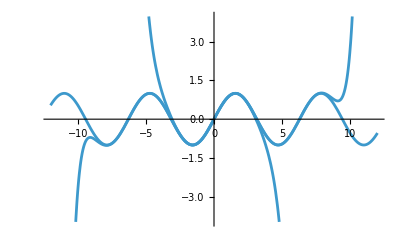

```mathematica
Sinf[x_, n_] = SetPrecision[Sum[(-1)^i x^(2i+1)/((2i+1)!),{i, 0, n}], MachinePrecision];                  (*Taylor series approximation*)
Plot[SetPrecision[{Sinf[x, 3], Sinf[x, 10], Sinf[x, 10000]}, MachinePrecision], {x, -12, 12}]
```

General::munfl: 19.764399001+1.0212814981×10^-2798 ⅈ is too small to represent as a normalized machine number; precision may be lost.

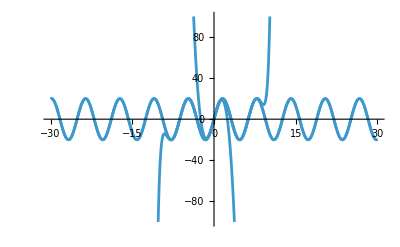

```mathematica
Plot[SetPrecision[Table[20*Sinf[x, 10^n], {n, 0, 3}], MachinePrecision], {x, -30, 30}, PlotRange -> 100]
```

```mathematica
Table[N[Sum[((10-Abs[(-10+(20/n x))])* Tan[60*(π/180)]+10)* (20/n)*20, {x, 0, n}]], {n, {1, 10, 100, 1000, 10000, 100000}}]    (*from the gabled house*)
```

{8000.,7864.1,7504.1,7468.1,7464.5,7464.14}

## 14. Convergence Tests

Based on our earlier definition of convergence, a series is only convergent if the terms approach 0. 
But, if the terms approach 0, this tells us nothing, as the sum  has terms that approach 0, even though it is divergent. 
This test is only designed for checking some divergent series.

Integral test
Integral: ∫_n_0^∞ a(x)ⅆx

must be a natural number.

must decrease as  increases.

must be positive for all .

must be continuous for all .

Limit comparison test

If  and  is divergent, then  is also divergent.
Otherwise,  is convergent.

Alternating Series Test
Sum: 
Conditions:  is non-negative for ,  is monotone decreasing(never increasing), and .
If all conditions hold, then  converges.

Ratio Test
The ratio test states that if the absolute value of the ratio between one term and the next is larger than 1(the series is increasing), then the series will diverge. Similarly, if it is less than 1, then the series will converge.
If the ratio is 1(no change between terms), then no conclusion can be made.

## 15. Volume of N-D sphere

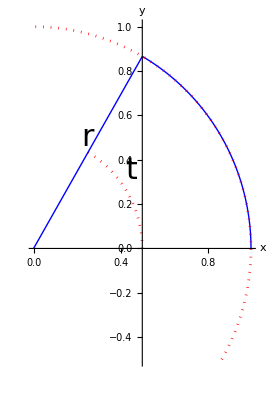

```mathematica
Clear[Circular, r, s, t, x]
Circular[r_, t_] = r * {Cos[t], Sin[t]};
SandT = ParametricPlot[Circular[1, x] , {x, 0, π/3}, Axes -> True, AxesLabel->{x,y}, AxesStyle->Thick, AxesOrigin->{0,0,0}, PlotStyle ->{{Thick,Blue},{Thick,Blue}}];
Labels = Graphics[{Text[Style[t, FontSize -> 30], {0.45, 0.35}], Text[Style[r, FontSize -> 30], {0.25, 0.5}]}];
ExtendedAxis = ParametricPlot[{Circular[0.5, x]} , {x, 0, π/3}, Axes -> True, AxesLabel->{x,y,z}, AxesStyle->Thick, AxesOrigin->{0,0,0}, PlotStyle ->{{Dotted,Red},{Dotted,Red}}];
ExtendedAxis2 = ParametricPlot[{Circular[1, x]} , {x, -π/6, π/2}, Axes -> True, AxesLabel->{x,y,z}, AxesStyle->Thick, AxesOrigin->{0,0,0}, PlotStyle ->{{Dotted,Red},{Dotted,Red}}];
LinesPlot = {Graphics[{Thick, Blue, Line[ {{0,0}, Circular[1, π/3]}]}]};
Show[ SandT, Labels, ExtendedAxis, ExtendedAxis2, LinesPlot, PlotRange -> All, ViewPoint->{3, 3, 3}]
```

```mathematica
Clear[Spherical, r, s, t, x] 
Spherical[r_, s_, t_] = r * {Sin[s] Cos[t], Sin[s] Sin[t], Cos[s]};
SandT = ParametricPlot3D[{Spherical[1, x, π/2], Spherical[1,π/2,x]} , {x, 0, π/3}, ViewPoint->{3, 3, 3}, Axes -> True, AxesLabel->{x,y,z}, AxesStyle->Thick, AxesOrigin->{0,0,0}, PlotStyle ->{{Thick,Blue},{Thick,Blue}}];
Labels = Graphics3D[{Text[Style[s, FontSize -> 30], {0, 0.5, 1}], Text[Style[t, FontSize -> 30], {1, 0.5, 0}], Text[Style[r, FontSize -> 30], {0.25, 0.5, 0.25}]}];
ExtendedAxis = ParametricPlot3D[{Spherical[1, x, π/2], Spherical[1,π/2,x]} , {x, -π/6, π/2}, ViewPoint->{3, 3, 3}, Axes -> True, AxesLabel->{x,y,z}, AxesStyle->Thick, AxesOrigin->{0,0,0}, PlotStyle ->{{Dotted,Red},{Dotted,Red}}];
LinesPlot = {Graphics3D[{Thick, Blue, Line[ {{0,0,0}, Spherical[1, π/3,π/3]}]}], Graphics3D[{Thick, Dashed, Red, Line[ {Spherical[1, π/2, π/3], Spherical[1, π/3,π/3]}]}], Graphics3D[{Thick, Dashed, Red, Line[ {Spherical[1, π/3, π/2], Spherical[1, π/3,π/3]}]}]};
Show[ SandT, Labels, ExtendedAxis, LinesPlot, PlotRange -> All, ViewPoint->{3, 3, 3}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Spherical[r, s, 0], {r, 2, 3}, {s, 0, 1}, ViewPoint->Front]
ParametricPlot3D[{r, s, 0}, {r, 2, 3}, {s, 0, 1}, ViewPoint->Top]
```

-Graphics3D-

-Graphics3D-

```mathematica
Clear[x, y, z, t, r, s, u, v, r, Second, p, s, q, v, u];
x[p_, s_, q_, v_, u_] = p Sin[u] Cos[q] Cos[s];
y[p_, s_, q_, v_, u_] = p Sin[u] Cos[q] Sin[s];
z[p_, s_, q_, v_, u_] = p Sin[u] Sin[q] Cos[v];
t[p_, s_, q_, v_, u_] = p Sin[u] Sin[q] Sin[v];
g[p_, s_, q_, v_, u_] = p Cos[u];
Clear[gradx, grady, gradz, Vxyz];
gradx[p_, s_, q_, v_, u_] = {D[x[p, s, q, v, u], p], D[x[p, s, q, v, u], s], D[x[p, s, q, v, u], q], D[x[p, s, q, v, u], v], D[x[p, s, q, v, u], u]};
grady[p_, s_, q_, v_, u_] = {D[y[p, s, q, v, u], p], D[y[p, s, q, v, u], s], D[y[p, s, q, v, u], q], D[y[p, s, q, v, u], v], D[y[p, s, q, v, u], u]};
gradz[p_, s_, q_, v_, u_] = {D[z[p, s, q, v, u], p], D[z[p, s, q, v, u], s], D[z[p, s, q, v, u], q], D[z[p, s, q, v, u], v], D[z[p, s, q, v, u], u]};
gradt[p_, s_, q_, v_, u_] = {D[t[p, s, q, v, u], p], D[t[p, s, q, v, u], s], D[t[p, s, q, v, u], q], D[t[p, s, q, v, u], v], D[t[p, s, q, v, u], u]};
gradg[p_, s_, q_, v_, u_] = {D[g[p, s, q, v ,u], p], D[g[p, s, q, v, u], s], D[g[p, s, q, v, u], q], D[g[p, s, q, v, u], v], D[g[p, s, q, v, u], u]};
Vxyz[p_, s_, q_, v_, u_] = Abs[Det[{gradx[p, s, q, v, u], grady[p, s, q, v, u], gradz[p, s, q, v, u], gradt[p, s, q, v, u], gradg[p, s, q, v, u]}]];
Integrate[Vxyz[p,s,q,v,u], {p, 0, r}, {s, 0, 2 Pi}, {q, 0, Pi/2}, {v, 0, Pi}, {u, 0, 2 Pi}]
```

(8 π^2 r^5)/15

WolframAlphaQueryResults

(8 π^2 r^5)/15≈5.26379 r^5
(assuming radius r)

```mathematica
Clear[v, n, d, r, R, x];
v[d_, r_] = π^(d/2)/Gamma[1+d/2] r^d;
Table[v[n, R] / v[n - 2, R], {n, 1, 30, 1}];
FindSequenceFunction[%, n]
```

(2 π R^2)/n

```mathematica
RSolveValue[{v[n]==2 Pi v[n-2]/n,v[2]==Pi,v[3]==4/3 Pi},v[n],n]
Table[%, {n, 2, 6}]
```

π^(n/2)/Gamma[1+n/2]

{π,(4 π)/3,π^2/2,(8 π^2)/15,π^3/6}

```mathematica
clear[SA, d, n, R, r, V];
SA[d_, r_] = (2 π^(d/2))/Gamma[d/2] r^(d-1);
V[d_, r_] = π^(d/2)/Gamma[1+d/2] r^d;
Table[SA[d, r], {d, 3, 10}]
Table[D[V[d, r], r], {d, 3, 10}]
```

{4 π r^2,2 π^2 r^3,(8 π^2 r^4)/3,π^3 r^5,(16 π^3 r^6)/15,(π^4 r^7)/3,(32 π^4 r^8)/105,(π^5 r^9)/12}

{4 π r^2,2 π^2 r^3,(8 π^2 r^4)/3,π^3 r^5,(16 π^3 r^6)/15,(π^4 r^7)/3,(32 π^4 r^8)/105,(π^5 r^9)/12}

```mathematica
Clear[Spherical, r, s, t, x]
Spherical[r_, s_, t_] = r * {Sin[s] Cos[t], Sin[s] Sin[t], Cos[s]};
ParametricPlot3D[Spherical[r, s, 0], {r, 0, 3}, {s, 0, 2π}, ViewPoint->Front]
ParametricPlot3D[Spherical[r, s, 0], {r, 2, 3}, {s, 0, 2π}, ViewPoint->Front]
ParametricPlot3D[Spherical[r, s, 0], {r, 2.8, 3}, {s, 0, 2π}, ViewPoint->Front]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Clear[V, R, r, n, ϵ]
ϵ = 0.1;
V[d_, r_] = π^(d/2)/Gamma[1+d/2] r^d;
Shell[d_, r_] = V[d, r] - V[d, r - (ϵ r)];
R = 10;
Table[Shell[d, R]/V[d, R], {d, 2, 16}]
```

{0.19,0.271,0.3439,0.40951,0.468559,0.521703,0.569533,0.61258,0.651322,0.686189,0.71757,0.745813,0.771232,0.794109,0.814698}